Длина кратчайшего пути: 113

Вершины кратчайшего пути: {1,9,10,11,12,13,21,22,30,38,46,45,44,52,60,61,62,63,64,63,62,61,53,52,44,36,28,20,19,18,10,2,1}

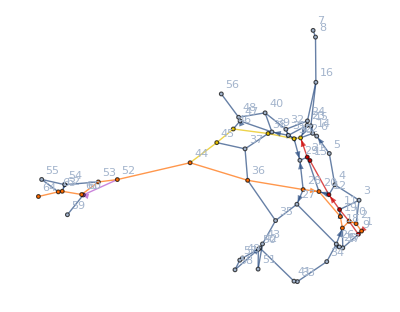

```mathematica
Ded={{25,17,2},{10,2,3},{26,18,5},{15,14,3},{50,42,1},{19,11,3},{23,22,4},{28,27,4},{28,20,4},{30,29,5},{1,9,3},{5,6,6},{11,12,4},{21,22,5},{12,20,3},{28,29,6},{30,31,2},{31,32,3},{47,48,2},{54,62,4},{31,39,4},{60,61,1}};

Ued={{1,2,2},{2,3,5},{9,17,4},{3,4,5},{4,5,4},{33,41,1},{7,8,2},{49,57,1},{9,10,3},{10,11,2},{10,18,2},{12,13,5},{26,34,3},{15,16,6},{50,58,6},{17,18,5},{3,11,6},{18,19,2},{19,20,6},{20,21,5},{27,35,3},{35,43,3},{43,51,5},{23,24,1},{25,26,1},{4,12,2},{26,27,6},{28,36,6},{36,44,6},{44,52,6},{52,60,5},{33,34,5},{13,21,1},{35,36,6},{21,29,2},{36,37,5},{37,38,4},{37,45,5},{38,39,1},{39,40,5},{53,61,5},{41,42,6},{6,14,1},{42,43,1},{14,22,2},{22,30,1},{44,45,4},{30,38,4},{45,46,3},{38,46,5},{46,47,2},{49,50,3},{50,51,6},{15,23,1},{23,31,5},{52,53,3},{53,54,5},{39,47,4},{54,55,5},{55,63,6},{57,58,3},{8,16,6},{16,24,6},{59,60,5},{24,32,6},{32,40,5},{61,62,3},{40,48,6},{62,63,1},{48,56,5},{63,64,4}};

{v1,v2,v3,v4}={1,64,22,52};

(*Edge lists*)
directedEdgeList=Map[Function[x,DirectedEdge[Part[x,1],Part[x,2]]],Ded];
undirectedEdgeList=Map[Function[x,UndirectedEdge[Part[x,1],Part[x,2]]],Ued];
(*subGraphs*)
directedSubgraph=Graph[directedEdgeList];
undirectedSubgraph=Graph[undirectedEdgeList];

(*graphs  union*)
graph=GraphUnion[directedSubgraph,undirectedSubgraph];

(*вес*)
For[i=1,i≤Length[Ded],i++,
graph=SetProperty[{graph,directedEdgeList⟦i⟧},EdgeWeight->Ded⟦i⟧⟦3⟧];
]

For[i=1,i≤Length[Ued],i++,
graph=SetProperty[{graph,undirectedEdgeList⟦i⟧},EdgeWeight->Ued⟦i⟧⟦3⟧];
]

graph=SetProperty[graph,VertexLabels->"Name"];
graph=SetProperty[graph,GraphLayout->{VertexLayout->{"SpringElectricalEmbedding","EdgeWeighted"->True}}];
graph;

(*Adjacency matrix*)
adjacencyMatrix=WeightedAdjacencyMatrix[graph];
(*Replace nulls*)
maxValue=Infinity;
For[i=1,i≤Length[adjacencyMatrix],i++,
For[j=1,j≤Length[adjacencyMatrix⟦i⟧],j++,
If[adjacencyMatrix⟦i⟧⟦j⟧==0,adjacencyMatrix⟦i⟧⟦j⟧=maxValue]
]
]

CalcPath[waMatrix_,startV_,finishV_]:=Module[{vertex,vertices,distances,pathVertices,path,v},
If[startV==finishV,Return[{0,{0}}];];
(*Путь v1->v2 Dijkstra*)
vertex=startV;
vertices={};
AppendTo[vertices,vertex];
(*Distance array init for starting vertex v1*)
distances={};
pathVertices={};

For[v=1,v≤Length[waMatrix⟦vertex⟧],v++,
AppendTo[pathVertices,vertex];
If[v==vertex,
AppendTo[distances,0];,
AppendTo[distances,adjacencyMatrix⟦vertex⟧⟦v⟧];

]
];

For[i=1,i<Length[distances],i++,
minValue=maxValue;

For[v=1,v<=Length[distances],v++,
If[!MemberQ[vertices,v]&&minValue>distances⟦v⟧,
minValue=distances⟦v⟧;
vertex=v;
];
];

AppendTo[vertices,vertex];
Clear[v];
(*diistances recalc*)
For[v=1,v<=Length[distances],v++,
waMatrix⟦vertex⟧⟦v⟧
If[!MemberQ[vertices,v],
If[distances⟦v⟧>distances⟦vertex⟧+waMatrix⟦vertex⟧⟦v⟧,pathVertices⟦v⟧=vertex];
distances⟦v⟧=Min[distances⟦v⟧,distances⟦vertex⟧+waMatrix⟦vertex⟧⟦v⟧];
;]
]
];
(*create path*)
path={};
v=finishV;
PrependTo[path,v];
While[v≠startV,
v=pathVertices⟦v⟧;
PrependTo[path,v];
];
outList={};
AppendTo[outList,distances⟦finishV⟧];
AppendTo[outList,path];
Return[outList]
]

GetSortedDistanceList[pathMatrix_,start_,vertexList_]:=Module[{i,j},
sortedDistanceList={};
For[i=1,i≤Length[vertexList],i++,
d=pathMatrix⟦start⟧⟦vertexList⟦i⟧⟧⟦1⟧;
dPair={vertexList⟦i⟧,d};
AppendTo[sortedDistanceList,dPair];
];
sortedDistanceList=SortBy[sortedDistanceList,Last];
Return[sortedDistanceList];
];

Pass[pathMatrix_,restVList_,startV_,currentV_,currentDistance_:0,currentPath_:{},minBranchPath_:{},minBranchDistance_:maxValue]:=Module[{k,dList,kRestVList,kCurrentDistance,kCurrentPath,branchPath,branchDistance,locMinBranchPath,locMinBranchDistance,resList,locResList},
resList={};
locMinBranchPath=minBranchPath;
locMinBranchDistance=minBranchDistance;

If[Length[restVList]==0,(*end  of the branch*)
retDist=pathMatrix⟦currentV⟧⟦startV⟧⟦1⟧;
If[locMinBranchDistance==maxValue||currentDistance+retDist<locMinBranchDistance,
(*modify min branch distance and path*)
locMinBranchDistance=currentDistance+retDist;
locMinBranchPath=currentPath;
AppendTo[locMinBranchPath,startV];
PrependTo[locMinBranchPath,startV];
];
AppendTo[resList,locMinBranchPath];
AppendTo[resList,locMinBranchDistance];
Return[resList];
];

dList=GetSortedDistanceList[pathMatrix,currentV,restVList];
For[k=1,k<=Length[dList],k++,
d=dList⟦k⟧⟦2⟧;
If[minBranchDistance==maxValue||minBranchDistance>currentDistance+d,
kCurrentDistance=currentDistance+d;
(*create rested vertex*)
kRestVList=dList;
kRestVList=Flatten[Map[First,kRestVList]];
kRestVList=Delete[kRestVList,k];
(*Append next vertex to current path*)
kCurrentPath=currentPath;
AppendTo[kCurrentPath,dList⟦k⟧⟦1⟧];

(*Function Return List*)
locResList={};
locResList=Pass[pathMatrix,kRestVList,startV,dList⟦k⟧⟦1⟧,kCurrentDistance,kCurrentPath,locMinBranchPath,locMinBranchDistance];
locMinBranchPath=locResList⟦1⟧;
locMinBranchDistance=locResList⟦2⟧;

];
];

AppendTo[resList,locMinBranchPath];
AppendTo[resList,locMinBranchDistance];
Return[resList];
](*END PASS*)

vList={1,64,22,52};
(*branches and constraints*)
(*Create  distance matrix*)
pathMatrix={};
For[m=1,m≤Length[vList],m++,
row={};
For[n=1,n≤Length[vList],n++,
AppendTo[row,CalcPath[adjacencyMatrix,vList⟦m⟧,vList⟦n⟧]];
];
AppendTo[pathMatrix,row];
];

(*indexing vertices*)
restVList={2,3,4};
shortestPathData=Pass[pathMatrix,restVList,1,1];
(*assembling whole path*)
chords=shortestPathData⟦1⟧;

pathVertexList={};
pathGraphs={};
For[i=1,i<Length[chords],i++,
(*Print[pathMatrix⟦chords⟦i⟧⟧⟦chords⟦i+1⟧⟧]*)
chord=pathMatrix⟦chords⟦i⟧⟧⟦chords⟦i+1⟧⟧⟦2⟧;
pathGraph=GraphUnion[PathGraph[chord],PathGraph[chord,{DirectedEdges->True}]];
AppendTo[pathGraphs,pathGraph];

If[i!=Length[chords]-1,chord=Delete[chord,Length[chord]]];
pathVertexList=Join[pathVertexList,chord];
]

Print["Длина кратчайшего пути: ",shortestPathData⟦2⟧]
Print["Вершины кратчайшего пути: ",pathVertexList]

(*show highlighted graph*)
highlightedGraph=HighlightGraph[graph,pathGraphs]
```